```mathematica
ClearAll["Global`*"]
```

```mathematica
tableL = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Impedance\\L3,3mH_2019_09_02_16_56_59.dat", {"Table","Data",All,{3,4}}];
```

```mathematica
newtableL = Delete[tableL, 1];
```

```mathematica
tableLS = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Impedance\\inductanceSubstituter_3,13mH_2019_09_03_10_16_13.dat", {"Table","Data",All,{3,4}}];
```

```mathematica
newtableLS = Delete[tableLS, 1];
tableLfixed = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Impedance\\L3,3mH_fixed1.dat", {"Table","Data",All,{3,4}}];
tableLSfixed=Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Impedance\\inductanceSubstituter_3,13mH_fixed.dat", {"Table","Data",All,{3,4}}];
```

```mathematica
ZparallelRC[R_, C_, ω_] := (R×1/(ⅈ×ω×C))/(R+1/(ⅈ×ω×C))
ZparallelRL[R_,L_,ω_]:=(R×ⅈ×ω×L)/(R+ⅈ×ω×L)
```

```mathematica
Zparallel3[R1_, R2_, R3_]:= (R1×R2×R3)/(R1×R2+R2×R3+R3×R1)
```

```mathematica
ZL[ω_, L_,Rp_, Cp_]:=50 + ZparallelRC[46.5, 25×10^-12, ω] + Zparallel3[50×10^3, (ⅈ×ω×L+0.5+ZparallelRL[Rp,0.0011,ω]), (1/(ⅈ×ω×Cp))]
```

```mathematica
Uin[ω_, L_, Rp_, Cp_]:=2×Re[Abs[ZparallelRC[46.5, 25×10^-12, 2×π×ω]]/Abs[ZL[2×π×ω,L, Rp, Cp]]]
```

```mathematica
fitL = FindFit[tableLfixed, Uin[ω, L,Rp, Cp], {{L, 2.03×10^-3},{Rp,160}, {Cp, 10^-11}}, ω, MaxIterations->1000]
```

{L→0.00195587,Rp→235.962,Cp→4.52936×10^-11}

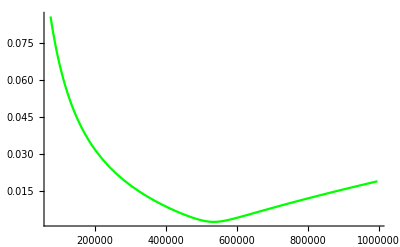

```mathematica
Show[ Plot[Uin[ω, L, Rp, Cp]/.fitL,{ω,0,Max[tableLfixed[[All,1]]]},PlotStyle->Green],ImageSize->Full,PlotRange->All]
```

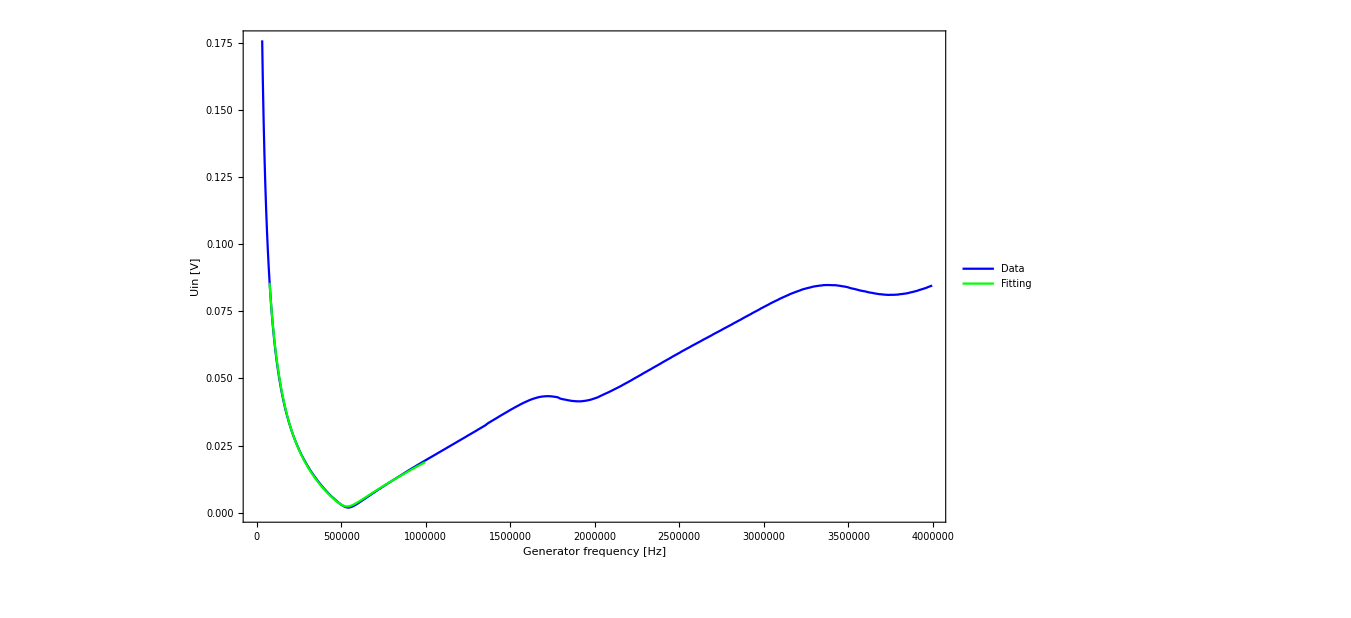

```mathematica
Legended[Show[ListLinePlot[tableL, PlotStyle->Blue],
Plot[Uin[ω, L, Rp, Cp]/.fitL,{ω,100,Max[tableLfixed[[All,1]]]},PlotStyle->Green],  Frame->{True,True,False,False},FrameLabel->{"Generator frequency [Hz]","Uin [V]"},ImageSize->1000, BaseStyle->{FontSize->24}],LineLegend[{Blue, Green},{"Data", "Fitting"}]]
```

```mathematica
fitLS = FindFit[tableLSfixed, Uin[ω, L, Rp, Cp], {{L, 2×10^-3}, {Rp, 236}, {Cp, 4.5×10^-11}}, ω,MaxIterations->1000]
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{L→0.00288661,Rp→76.8939,Cp→3.68664×10^-11}

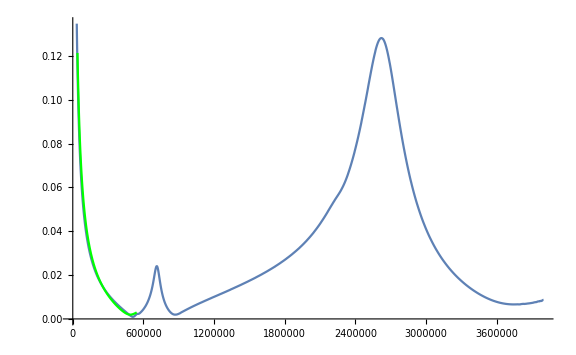

```mathematica
Show[ListLinePlot[newtableLS], Plot[Uin[ω,L,Rp, Cp]/.fitLS,{ω,Min[newtableLS[[All,1]]],Max[tableLSfixed[[All,1]]]},PlotStyle->Green],ImageSize->Large]
```

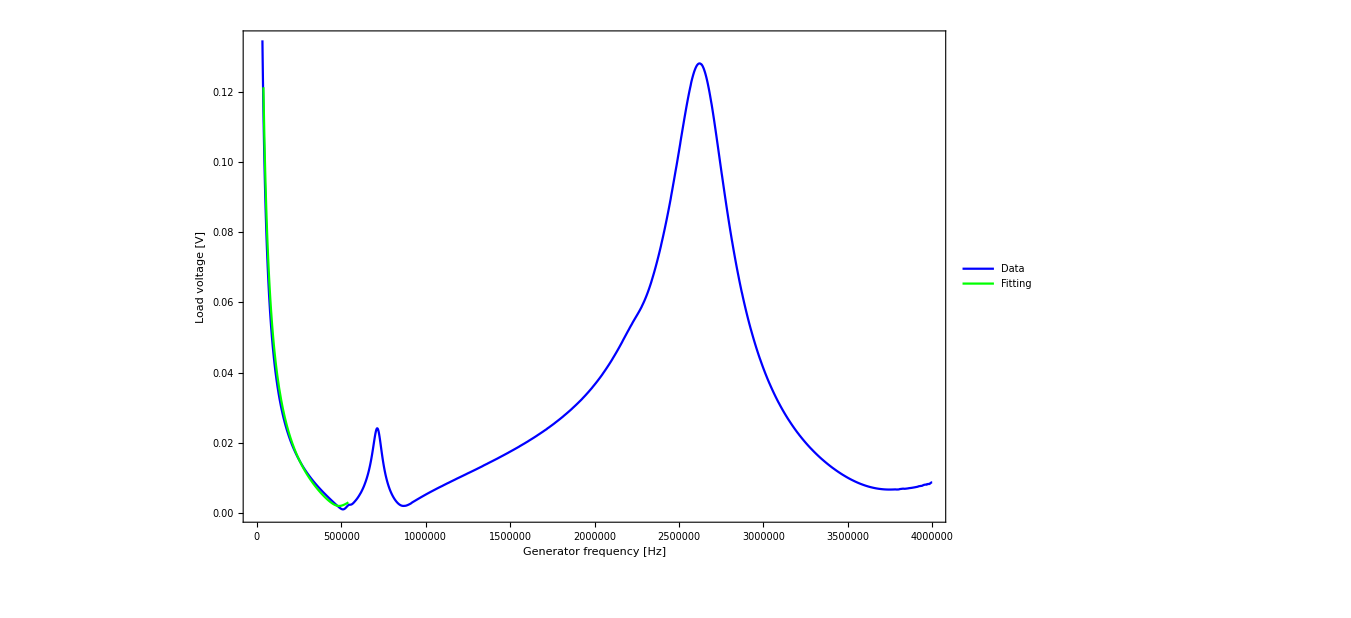

```mathematica
Legended[Show[ListLinePlot[newtableLS, PlotStyle->Blue],
Plot[Uin[ω, L, Rp, Cp]/.fitLS,{ω,Min[newtableLS[[All,1]]],Max[tableLSfixed[[All,1]]]},PlotStyle->Green],  Frame->{True,True,False,False},FrameLabel->{"Generator frequency [Hz]","Load voltage [V]"},ImageSize->1000, BaseStyle->{FontSize->24}],LineLegend[{Blue, Green},{"Data", "Fitting"}]]
```

```mathematica
NonlinearModelFit
```

NonlinearModelFit